```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
EngineeringForm[2*PlanckConstantReduced/(88.84163013814255*10^(-12)*ElectronCharge)]
```

((14.8176×10^-6) Joule Second)/Coulomb

```mathematica
1/(1/175.34+1/180.09)
```

88.8416

```mathematica
(PlanckConstant/ElectronCharge)*(10^10/(5.4*10^-3))*(340*2*2*Sqrt[2*Log[2]])*10^(-6)
```

(2.96533×10^9 PlanckConstant)/ElectronCharge

```mathematica
1.498*10^10-2.608*10^10
```

-1.11×10^10

Gaussian beam curvature

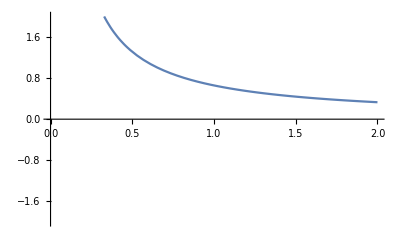

```mathematica
R[z_,w0_]:=z*(1+(π*w0^2/(785*10^(-9)*z))^2)
Plot[R[z*10^(-3),80*10^(-6)],{z,0,2},PlotRange->2]
```

Beam waist after lens = 2λ/π  f/d

```mathematica
EngineeringForm[2*785*10^(-9)/π*0.1/0.001]
```

49.9747×10^-6

```mathematica
Manipulate[

λ0=633*10^(-9);
n=1;

Am=1;
Bm=0;
Cm=1/f;
Dm=1;

qin[z_]:=z + ⅈ*π*n*w0^2/λ0;
qout[z_]:=(qin[z]*Am+Bm)/(qin[z]*Cm+Dm);
R[z_,w0_]:=z*(1+(π*w0^2/(λ0*z))^2);
w0f=Sqrt[Im[qout[0]]*λ0/(π*n)];
EngineeringForm[w0f];
Plot[R[z,w0f],{z,-0.004,0.004},PlotRange->{-0.2,0.2}],
{{w0,0.002},0,0.1},{{f,0.1},0,1}]
```

```mathematica
qout[0]
```

0.0999975+0.000503713 ⅈ

0.0000100744